# Polar Alignment Calculations

## Problem Statement

Wish to polar align a telescope. Assume that the polar axis of the scope is pointed at Dec = Dpa, and Ha = Hpa. Now consider taking an image at some location in the sky p1 = (H1, D1), then rotating the scope by an angle θ around this axis and taking a new image found to be at location p2 =  (H2, D2). We wish to solve for Dpa and Hpa.

We will create an axis system with Z pointing at the North Celestial Pole, and Y aligned with the meridian, and X perpendicular to the two axes.

-Graphics- -Graphics- -Graphics-

So process: from platesolved RA and DEC, calculate HA from LST. Use this to work out 3D vectors for P1 and P2 and work out the vector P1 -> P2. This direction defines the great circle plane that contains the telescope axis. Then search for a location on the great circle plane so that the angle between the two points is the rotation between the two positions AS MEASURED BY THE TELESECOPE.

We will create an axis system with Z pointing at the North Celestial Pole, and Y aligned with the meridian, and X perpendicular to the two axes.

## Clear data and set up vectors for the polar axis, P1 and P2

```mathematica
Remove["Global`*"];
pa = {Cos[Dpa] Sin[Hpa], Cos[Dpa] Cos[Hpa], Sin[Dpa]};
p1 = {Cos[D1] Sin[H1], Cos[D1] Cos[H1], Sin[D1]};
p2 =  {Cos[D2] Sin[H2], Cos[D2] Cos[H2], Sin[D2]};
```

## Set up rotation matrix to rotate from p1 to p2

```mathematica
rotn = RotationMatrix[θ, pa]
```

Format was still too complicated from inbuilt RotationMatrix, so used an alternative form below. Tested to make sure both gave same answers for numerical angles, so used simpler form below.

## Set up Alernative Form of Matrix

```mathematica
c1 = pa[[1]];
c2= pa[[2]];
c3 = pa[[3]];
```

```mathematica
m1 = Cos[θ] IdentityMatrix[3];
m2 =  (1 - Cos[θ]) {{c1 c1, c1 c2, c1 c3}, {c2 c1, c2 c2, c2 c3}, {c3 c1, c3 c2, c3 c3}};
m3 = Sin[θ]{{0, -c3, c2}, {c3, 0, -c1}, {-c2, c1, 0}};
m = m1 + m2 +m3
```

{{Cos[θ]+Cos[Dpa]^2 (1-Cos[θ]) Sin[Hpa]^2,Cos[Dpa]^2 Cos[Hpa] (1-Cos[θ]) Sin[Hpa]-Sin[Dpa] Sin[θ],Cos[Dpa] (1-Cos[θ]) Sin[Dpa] Sin[Hpa]+Cos[Dpa] Cos[Hpa] Sin[θ]},{Cos[Dpa]^2 Cos[Hpa] (1-Cos[θ]) Sin[Hpa]+Sin[Dpa] Sin[θ],Cos[Dpa]^2 Cos[Hpa]^2 (1-Cos[θ])+Cos[θ],Cos[Dpa] Cos[Hpa] (1-Cos[θ]) Sin[Dpa]-Cos[Dpa] Sin[Hpa] Sin[θ]},{Cos[Dpa] (1-Cos[θ]) Sin[Dpa] Sin[Hpa]-Cos[Dpa] Cos[Hpa] Sin[θ],Cos[Dpa] Cos[Hpa] (1-Cos[θ]) Sin[Dpa]+Cos[Dpa] Sin[Hpa] Sin[θ],Cos[θ]+(1-Cos[θ]) Sin[Dpa]^2}}

## Try Solving general problem

Calculate p1 rotated by m and see if we can solve for Hpa and Dpa  when rotated p1 = p2 - unable to solve given the complexity of the equations

```mathematica
p1r = m.p1;
(*Assuming[Dpa ∈ Reals && Hpa ∈ Reals && D1∈ Reals && H1 ∈ Reals && D2 ∈ Reals && H2 ∈ Reals, Solve[p1r[[3]] == p2[[3]] && p1r[[2]] == p2[[2]], {Hpa, Dpa}]];*)
```

Also tried for the original form of the matrix  - same problem

```mathematica
p1rs = rotns.p1;
(*Assuming[Dpa ∈ Reals && Hpa ∈ Reals && D1∈ Reals && H1 ∈ Reals && D2 ∈ Reals && H2 ∈ Reals, Solve[p1rs[[3]] == p2[[3]] && p1rs[[2]] == p2[[2]], {Hpa, Dpa}]];*)
```

## Try numerical solution

Try solving numerically for some typical values - first substitutions set up the misaligned polar axis, second set set up the first point. This is then to be rotated about PA through θ = 45 degrees (v2).

V2a is an analytic expression when D1, H1 and θ are known,  but the position of the polar axis is not. From knowing P1, P2 (=v2 here) can we numerically solve for Dpa and Hpa?

```mathematica
pavals = {Dpa -> 85.8°, Hpa -> 15.0°};
p1vals = {D1 -> 60°, H1 -> 0°};
```

```mathematica
v2 = m.p1 /. p1vals /. pavals /. θ -> 45°;
v2a = m.p1  /. p1vals /. θ -> 45° ;
```

```mathematica
(*NSolve[v2[[1]] == v2a[[1]] && v2[[3]] == v2a[[3]], {Dpa, Hpa}]*)
```

## Try solution described above

Now try solving according to the scheme above: 
	v1 is vector of P1, 
	v2 is vector of P2 (calculated above)
	dv is difference in two vectors
	dva is unit vector in direction of dv
	sz = sin of angle between horizon and dva
	cz = cos of angle between horizon and dva
	phi = azimuthal direction of dva

```mathematica
v1 = p1 /. p1vals;
dv = v2 - v1;
dva = dv / Sqrt[dv.dv];
sz = dva[[3]];
cz = Sqrt[1-dva[[3]]^2];
phi = ArcTan[dva[[1]], dva[[2]]];
```

Want to create equation for great circle perpendicular to dva. Start by creating unit circle in the y-z plane, then rotate around the y-axis so that the height of the transformed x-axis matches the z-value of dva. Second rotation around z to align transformed x-axis with dva.

```mathematica
gc  = {0, Sin[ϕ], Cos[ϕ]}
```

{0,Sin[ϕ],Cos[ϕ]}

Below are transformation matrices which accomplish that rotation.

```mathematica
Ry = {{cz, 0, -sz}, 
{0, 1, 0},
{sz, 0, cz}};
Rz = {{Cos[phi], -Sin[phi], 0},
{Sin[phi], Cos[phi], 0},
{0, 0, 1}};
```

Check that the rotated great circle is perpendicular to dva:

```mathematica
(Rz.Ry .gc) . dva//Simplify
```

5.55112×10^-17 Sin[ϕ]

Yes it is! Now create the equations for the rotated great circle:

```mathematica
gcc = (Rz.Ry.gc);
```

Now want to find out angle between P2 -> and A ->P2. Do that by creating the cross product of gcc and v1, and gcc and v2, then taking the dot product and convert the cross products to unit vectors.

```mathematica
a1 = Cross[gcc, v1];
a2 = Cross[gcc,v2];
cosang = a1.a2/Sqrt[(a1.a1) (a2.a2)];
```

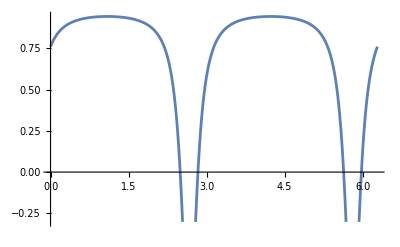

```mathematica
Plot [cosang, {ϕ, 0, 2 Pi}]
```

Now need to solve for the dot product equal to the cosine of the rotation angle - see figures above - and set to 45 degrees earlier.

```mathematica
asoln = Solve[cosang == Cos[Pi/4], ϕ]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ϕ→-0.901961},{ϕ→-0.056447},{ϕ→2.23963},{ϕ→3.08515}}

There are four solutions - we want the one with the smallest angle - we are supposed to be close to the pole. Check that the solution reproduces the vector values of pa:

```mathematica
pasoln = gcc /. asoln[[2]]
pa/.pavals
pasoln - pa/.pavals
```

{0.0189554,0.0707427,0.997314}

{0.0189554,0.0707427,0.997314}

{-3.96211×10^-15,8.03524×10^-15,-4.44089×10^-16}

It does, now calculate the solution for Dec and HA of the polar axisL:

```mathematica
decpas = ArcSin[pasoln[[3]]]*180/Pi
```

85.8

```mathematica
hapas = ArcTan[pasoln[[2]], pasoln[[1]]]*180/Pi
```

15.

Have managed to recreate solution as required!

```mathematica
VectoHADec[passoln]
```

VectoHADec[passoln]

```mathematica
VectoAltAz[pa/.pavals]
```

VectoAltAz[{0.0189554,0.0707427,0.997314}]

```mathematica
0.0010341649740236688*180/Pi
```

0.0592533

```mathematica
v2
```

{-0.304291,0.360574,0.881699}

```mathematica
ArcSin[v2[[3]]]*180/Pi
```

61.848

```mathematica
ArcTan[v2[[2]], v2[[1]]]*12/Pi
```

-2.67742

```mathematica
p0 = p1/.p1vals
```

{0,1/2,(√3)/2}

```mathematica
ArcSin[p0[[3]]]*180/Pi
ArcTan[p0[[2]], p0[[1]]]*180/Pi
```

60

0

## Alternative numerical solution

Try alternative to cross product where we calculate the component of the vectors v1 and v2 which are perpendicular to tpa and look at the angle between them.

```mathematica
a1a = v1 - gcc.v1 gcc;
a2a = v2 - gcc.v2 gcc;
cosanga = a1a.a2a/Sqrt[(a1a.a1a) (a2a.a2a)];
```

```mathematica
Plot [cosang, cosanga, {ϕ, 0, 2 Pi}]
```

Plot::nonopt: Options expected (instead of {ϕ,0,2 π}) beyond position 2 in Plot[cosang,cosanga,{ϕ,0,2 π}]. An option must be a rule or a list of rules.

Plot[cosang,cosanga,{ϕ,0,2 π}]

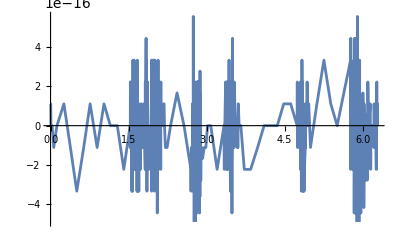

```mathematica
Plot[{cosang -cosanga},{ϕ,0,2 π}]
```

Yes, gives identical results!